```mathematica
(*Note: there are 4 parts. run each parts.*)
Clear[x,y,SS,g,t];
SS= DSolve[{y''[x]==y[x],y'[0]==0},y[x],x]
```

{{y[x]→ⅇ^-x (1+ⅇ^(2 x)) C[1]}}

```mathematica
g[x_]=y[x]/.SS[[1]]
```

ⅇ^-x (1+ⅇ^(2 x)) C[1]

```mathematica
t[x_]=Table[g[x]/.C[1]->j,{j,1,10}]
```

{ⅇ^-x (1+ⅇ^(2 x)),2 ⅇ^-x (1+ⅇ^(2 x)),3 ⅇ^-x (1+ⅇ^(2 x)),4 ⅇ^-x (1+ⅇ^(2 x)),5 ⅇ^-x (1+ⅇ^(2 x)),6 ⅇ^-x (1+ⅇ^(2 x)),7 ⅇ^-x (1+ⅇ^(2 x)),8 ⅇ^-x (1+ⅇ^(2 x)),9 ⅇ^-x (1+ⅇ^(2 x)),10 ⅇ^-x (1+ⅇ^(2 x))}

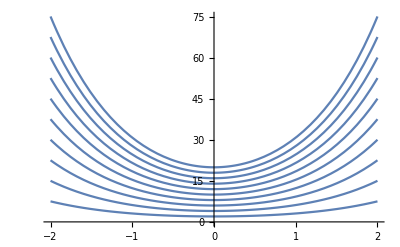

```mathematica
Plot[t[x],{x,-2,2}]
```